# q q̄→μ μ in EW theory (SM ): gauge invariance Vertices/Self en.

### PROCESS:

```mathematica
CKM = IndexDelta;
Neglect[MU] = Neglect[MU2] = 0;
Neglect[MM] = Neglect[MM2] = 0;
Neglect[mgamma]=0;
process ={-F[3, {1}], F[3, {1}]} -> {-F[2, {2}], F[2, {2}]} ;

SetOptions[InsertFields,  Model -> "SM",InsertionLevel->{Particles}, Restrictions -> NoLightFHCoupling];
SetOptions[CalcFeynAmp,PaVeReduce->True];
SetOptions[CreateFeynAmp, GaugeRules -> {GaugeXi[Z] -> ZGAUGE, GaugeXi[A] -> AGAUGE,
 GaugeXi[W] -> WGAUGE} ];
```

## SM: Feynman rules and Diagrams

Definisco valori di cariche e masse sostituite poi nei passaggi finali

```mathematica
CHARGESZl={QZLl->-1,QZUl->2/3,QZDl->-1/3,I3D->-1/2,I3L->-1/2,I3N->1/2,I3U->1/2}
CHARGESZr={QZLr->-1,QZUr->2/3,QZDr->-1/3}
CHARGESphl={QLl->-1,QUl->2/3,QDl->-1/3}
CHARGESphr={QLr->-1,QUr->2/3,QDr->-1/3}
MASSES={MU->0,MU2->0,MM->0,MM2->0,S+T+U->0}
MGAMMA0={mgamma->0,_mgamma->0};
```

{QZLl→-1,QZUl→2/3,QZDl→-1/3,I3D→-1/2,I3L→-1/2,I3N→1/2,I3U→1/2}

{QZLr→-1,QZUr→2/3,QZDr→-1/3}

{QLl→-1,QUl→2/3,QDl→-1/3}

{QLr→-1,QUr→2/3,QDr→-1/3}

{MU→0,MU2→0,MM→0,MM2→0,S+T+U→0}

```mathematica
(*GENERALIZZAZIONE CARICHE/ISOSPIN PER CASO SM*)
coupling[x_]:=Module[{Mcouplin,chargenuZ,chargelepZ,chargeupZ,chargedownZ,n,m,chargenup,chargelep,chargedown,chargeup},

Mcouplin=M$CouplingMatrices;
(*____________________________  Z COUPLING  ______________________________*)
(*neutrino*)
chargenuZ[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[2]])==rhs_]:=
lhs==(rhs/.{
	dZZZ1-> 2 I3N dZZZ1,
	1/(2 CW SW)->I3N/(CW SW),
	EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
	

});
chargenuZ[other_]=other;
Mcouplin=chargenuZ/@Mcouplin;

(*lepton*)
chargelepZ[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3L*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			SW/CW->-QZLl SW/CW,
			(-1/2+SW^2)->(I3L-QZLl*SW^2),
			dZAZ1->- QLl dZAZ1 (*CT misto gamma Z*)
			},
		rhsR/.{
		SW/CW->-QZLr SW/CW,
		dZAZ1->- QLr dZAZ1 (*CT misto gamma Z*)
		}
});
chargelepZ[other_]=other;
Mcouplin=chargelepZ/@Mcouplin;

(*q up*)
chargeupZ[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3U*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(1/2-2/3SW^2)->(I3U-QZUl*SW^2),
			
			dZAZ1->3/2 QUl dZAZ1,(*CT misto gamma Z: − δ [g1,g2] QU δZ(γZ)/2*)
			-2/3->-QZUl},
		rhsR/.{
			-dZAZ1 /3->-QUr*dZAZ1 /2, (*CT misto gamma Z*)
			-1/3 I*EL->-QZUr/2 I*EL,
			-2/3*I->-QZUr*I,
			-2/3->-QZUr,
			-SW /(3*CW)->-QZUr*SW /(2*CW)}
});
chargeupZ[other_]=other;
Mcouplin=chargeupZ/@Mcouplin;

(*q down*)
chargedownZ[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{
			-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3D*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),
			dZAZ1->-3 QDl dZAZ1, (*CT misto gamma Z*)
			1/3->-QZDl},
			
		rhsR/.{
			dZZZ1->- 3 QZDr*dZZZ1 ,
			dZAZ1->- 3 QDr*dZAZ1 ,(*CT misto gamma Z*)
			1/3 I*EL->-QZDr I*EL,
			1/3*I->-QZDr*I,
			1/3->-QZDr,
			SW /(3*CW)->-QZDr*SW /(CW)}
});
chargedownZ[other_]=other;
Mcouplin=chargedownZ/@Mcouplin;

(*____________________________  GAMMA COUPLING  ___________________________*)
(*neutrino*)
chargenup[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[1]])==rhs_]:=
lhs==(rhs/.{
		EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
});
chargenup[other_]=other;
Mcouplin=chargenup/@Mcouplin;
(*lepton*)
chargelep[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+SW^2)->(I3L-QZLl*SW^2)/-QLl,(*CT misto gamma Z*)
			I->-QLl*I,
			1/2*I->-1/2 QLl*I
},
			
		rhsR/.{dZZA1->- QZLr dZZA1/-QLr,(*CT misto gamma Z*)
		I->-QLr*I,
			1/2*I->-1/2 QLr*I
		}
});
chargelep[other_]=other;
Mcouplin=chargelep/@Mcouplin;

(*q up*)
chargeup[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(1/2-2/3SW^2)->(I3U-QZUl*SW^2),(*CT misto gamma Z*)
			-2/3->-QUl,
			-2/3*I->-QUl*I},
			
		rhsR/.{dZZA1->3/2 QZUr dZZA1,(*CT misto gamma Z*)
		-2/3->-QUr,
		-2/3*I->-QUr*I}
});
chargeup[other_]=other;
Mcouplin=chargeup/@Mcouplin;

(*q down*)
chargedown[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),(*CT misto gamma Z*)
			1/3->-QDl,
			1/3*I->-QDl*I
			},
							
	rhsR/.{ dZZA1->-3 QZDr dZZA1,(*CT misto gamma Z*)
			1/3->-QDr,
			1/3*I->-QDr*I}
});
chargedown[other_]=other;
Mcouplin=chargedown/@Mcouplin;

Mcouplin
];
```

```mathematica
InitializeModel["SM",
ModelEdit :>{
M$ClassesDescription=M$ClassesDescription//.{(-Charge)->QL Charge,(2/3Charge)->QU Charge,(-1/3Charge)->QD Charge(*,
M$ClassesDescription[[5,2,3,2]]->mgamma*)},
M$CouplingMatrices=coupling[M$CouplingMatrices]}

];
```

loading generic model file /home/arianna/Documenti/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/arianna/Documenti/FeynArts-3.11/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

## Tree Level

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 18 field point(s)

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams



FeynArtsGraphics[][([1] | [2])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-33.frm

running FORM...

ok

```mathematica
tops = CreateTopologies[0, 2 -> 2];
ins = InsertFields[tops, process];
Paint[ins,ColumnsXRows->{2,1},Numbering->Simple,
SheetHeader->None,ImageSize->{512,256}]
born1=CreateFeynAmp[ins]//.MGAMMA0;
born = CalcFeynAmp[born1];
```

## Self Energies

```mathematica
tops2 = CreateTopologies[1, 2 -> 2, SelfEnergiesOnly];
ins2 = InsertFields[tops2, process];
ins2 = DiagramSelect[ins2, FreeQ[#, Field[5|6] -> S]&];
Paint[ins2,ColumnsXRows->{11,7},Numbering->Simple,
SheetHeader->None,ImageSize->{1212,756}]
selfff=CreateFeynAmp[ins2];
```

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 10 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 65 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

Restoring 18 field point(s)

in total: 75 Particles insertions

> Top. 1 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 2 aebe/cfdf/egfhghgh.m, 0 diagrams

-Graphics-

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5] | [6] | [7] | [8] | [9] | [10] | [11]
[12] | [13] | [14] | [15] | [16] | [17] | [18] | [19] | [20] | [21] | [22]
[23] | [24] | [25] | [26] | [27] | [28] | [29] | [30] | [31] | [32] | [33]
[34] | [35] | [36] | [37] | [38] | [39] | [40] | [41] | [42] | [43] | [44]
[45] | [46] | [47] | [48] | [49] | [50] | [51] | [52] | [53] | [54] | [55]
[56] | [57] | [58] | [59] | [60] | [61] | [62] | [63] | [64] | [65] | [66]
[67] | [68] | [69] | [70] | [71] | [72] | [73] | [74] | [75] | Null | Null)]

creating amplitudes at level(s) {Particles}

> Top. 1: 10 Particles amplitudes

> Top. 2: 65 Particles amplitudes

in total: 75 Particles amplitudes

#### Calcolo feynamp

```mathematica
self=CalcFeynAmp[Take[selfff,{1,20}]//.MGAMMA0][[1]];
self1=CalcFeynAmp[Take[selfff,{21,30}]//.MGAMMA0][[1]];
self2=CalcFeynAmp[Take[selfff,{31,41}]//.MGAMMA0][[1]];
self3=CalcFeynAmp[Take[selfff,{42,47}]//.MGAMMA0][[1]];
self8=CalcFeynAmp[Take[selfff,{48,52}]//.MGAMMA0][[1]];
self4=CalcFeynAmp[Take[selfff,{53,63}]//.MGAMMA0][[1]];
self5=CalcFeynAmp[Take[selfff,{64,70}]//.MGAMMA0][[1]];
```

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-33.frm

running FORM...

ok

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-33.frm

running FORM...

ok

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-33.frm

running FORM...

ok

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-33.frm

running FORM...

ok

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-33.frm

running FORM...

ok

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-33.frm

running FORM...

ok

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-33.frm

running FORM...

ok

```mathematica
self6=CalcFeynAmp[Take[selfff,{71,74}]//.MGAMMA0][[1]];
```

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-33.frm

running FORM...

ok

```mathematica
self7=CalcFeynAmp[Take[selfff,{75}]//.MGAMMA0][[1]];
```

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-33.frm

running FORM...

ok

```mathematica
selftot=self+self1+self2+self3+self4+self5+self6+self7+self8;
```

### UV divergent part Self-energies:

```mathematica
selftot1=Unabbr[selftot];
provvself=Collect[%,WeylChain[__]];
```

```mathematica
selfdiv= UVDivergentPart[selftot];
provaself = Unabbr[SSSSS*selfdiv] ;
```

## Vertices

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 7 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 8 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

Restoring 18 field point(s)

in total: 15 Particles insertions

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdg/ghefehfh.m, 0 diagrams

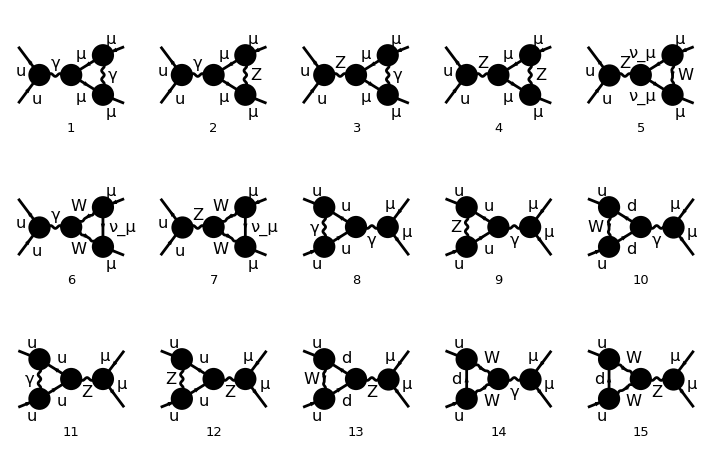

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-33.frm

running FORM...

ok

```mathematica
tops4 = CreateTopologies[1, 2 -> 2, TrianglesOnly];
ins4 = InsertFields[tops4, process];
ins4 = DiagramSelect[ins4, FreeQ[#, Field[5] -> S]&];
Paint[ins4,ColumnsXRows->{5,3},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
verttt=CreateFeynAmp[ins4];
vert = CalcFeynAmp[verttt//.MGAMMA0];
```

```mathematica
verttot=vert[[1]];
```

### UV divergent part Vertices:

```mathematica
verttot1=Unabbr[verttot];
provvert=Collect[%,WeylChain[__]];
```

```mathematica
vertdiv = UVDivergentPart[verttot];
provavert = Unabbr[VVVVV *vertdiv] ;
```

## Boxes

```mathematica
tops5 = CreateTopologies[1, 2 -> 2, BoxesOnly];
ins5 = InsertFields[tops5, process];
(*Paint[ins5,ColumnsXRows->{3,3},Numbering->Simple,
SheetHeader->None,ImageSize->{612,556}]*)
box1=  CreateFeynAmp[ins5];
```

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 4 Particles insertions

> Top. 8: 5 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

Restoring 18 field point(s)

in total: 9 Particles insertions

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 5 Particles amplitudes

in total: 9 Particles amplitudes

## Counterterms (CT)

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 4 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

Restoring 18 field point(s)

in total: 8 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebe/cfdf/gegf.m, 0 diagrams

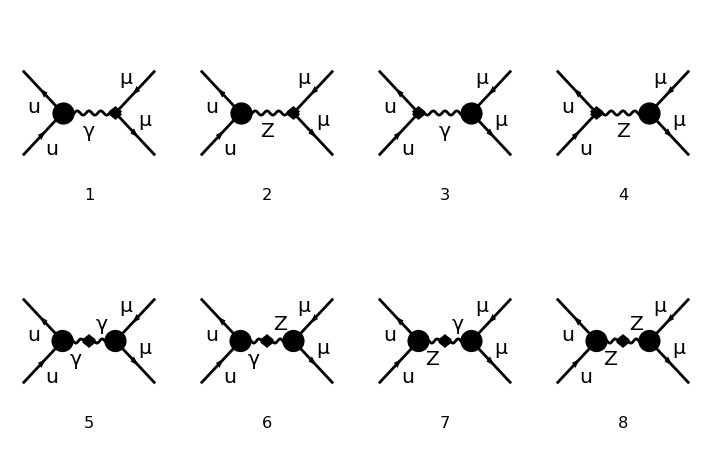

FeynArtsGraphics[][([1] | [2] | [3] | [4]
[5] | [6] | [7] | [8])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 4 Particles amplitudes

in total: 8 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-33.frm

running FORM...

ok

```mathematica
tops1 = CreateCTTopologies[1, 2 -> 2,
  ExcludeTopologies -> {TadpoleCTs,WFCorrectionCTs (*loop counterterms*)}];
ins1 = InsertFields[tops1, process];
Paint[ins1,ColumnsXRows->{4,2},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
counter = CreateFeynAmp[ins1];
ct=CalcFeynAmp[counter];
counterterms = Unabbr[ct];
```

```mathematica
(*set variabili semplificate*)
mzg=Times[MZ,Power[ZGAUGE,Rational[1,2]]];
mwg=Times[MW,Power[WGAUGE,Rational[1,2]]];
P1=FourMomentum[Incoming,1];
P2=FourMomentum[Incoming,2];
Q1=FourMomentum[Internal,1];
K1=FourMomentum[Outgoing,1];
K2=FourMomentum[Outgoing,2];
```

```mathematica
(*funzioni prodotto scalare e levicivita*)
SetAttributes[SP,Orderless];
SP/:SP[Index[u__],Index[v__]] SP[p_,Index[u__]] := SP[p,Index[v]];
SP/:SP[a_,Index[mu__]]^2 := SP[a,a];
SP/:SP[a_,Index[mu__]] SP[b_,Index[mu__]] := SP[a,b];
SP/:SP[Index[mu__],Index[mu__]] = d;
SP/:SP[Index[mu__],Index[nu__]]^2 = d;
SP/:SP[-b_,a_]:=-SP[b,a];
SP/:SP[DiracSlash[w_],x_]:=SP[w,x];
SP/:SP[DiracMatrix[w_],x_]:=SP[w,x];
(*levicivita product. 4 indices (d->4)*)
```

```mathematica
SP/:SP[P1,P1]:=0;
SP/:SP[P2,P2]:=0;
SP/:SP[K2,K2]:=MM2;
SP/:SP[K1,K1]:=MM2;
SP/:SP[P1,P2]:=S/2;
SP/: SP[K1,K2]:=S/2-MM2;
SP/: SP[P1,K1]:=(MM2-T)/2;
SP/: SP[P2,K2]:=(MM2-T)/2; 
SP/:SP[P1,K2]:=(MM2-U)/2; SP/:SP[P2,K1]:=(MM2-U)/2;
```

## Renormalization Constants (RC)

```mathematica
rc=CalcRenConst[counterterms];
```

```mathematica
fff=Table[rc[[1,i]]//Simplify,{i,1,Length[rc[[1]]]}]//.{QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr}//.{QUl->QU,QLl->QL,QUr->QU,QLr->QL,QDl->QD,QDr->QD};
```

```mathematica
ggg1=fff[[1]]//.IGram'[x_]->-IGram[x]^2//.IGram[x_]->1/x//.Re[x_]->x//.{Den[S,x_] -> 1/(S-x),Den[MZ2,x_]->1/(MZ2-x),Den[MW2,x_]->1/(MW2-x)}//.B0i[bb0,MW2,0,MW2]->A0[MW2]/MW2+1//Simplify;
```

```mathematica
Coefficient[ggg1[[2]],AGAUGE]//Simplify
```

-(Alfa (1+Finite) MW2 Pair[k[1],nul]^2)/(4 π (-MW2 Pair[nul,nul]+Pair[k[1],nul]^2))

## GAUGE INDEPENDENCE

```mathematica
(*COUNTERTERMS:i dZZZ1|dZAA1|dZAZ1|dZZA1 dei campi interni si cancellano quando sommo tutti i contributi nei CT*)
```

```mathematica
Collect[ExpandSums[counterterms[[1]]//.IGram'[x_]->-IGram[x]^2//.{IGram[x_]->1/x,
Conjugate[x_]->x ,Re[x_]->x}(*//.MASSES*)//.{QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr}//.{QUl->QU,QLl->QL,QUr->QU,QLr->QL,QDl->QD,
QDr->QD}//. {Den[S,x_] -> 1/(S-x),Den[MZ2,x_]->1/(MZ2-x),Den[MW2,x_]->1/(MW2-x) }],WeylChain[__],Simplify]
MemberQ[%,dZZZ1|dZAA1|dZAZ1|dZZA1,Infinity]
```

-1/(CW2^2 (MZ2-S)^2 S)8 Alfa π QL QU (2 dSW1 S (-MZ2+S) SW+CW2^2 (MZ2-S)^2 (2 dZe1+dZfR1[2,2,2]+dZfR1[3,1,1])+CW2 S SW2 (dMZsq1-(MZ2-S) (2 dZe1+dZfR1[2,2,2]+dZfR1[3,1,1]))) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|u̇ 4)) ((u2|6|v3))-1/(CW2^2 (MZ2-S)^2 S SW SW2)8 Alfa π (2 dSW1 (MZ2-S) S SW2 (QL (I3U-QU) SW2+I3L (-I3U+QU SW2))+CW2^2 QL QU (MZ2-S)^2 SW SW2 (2 dZe1+dZfL1[2,2,2]+dZfL1[3,1,1])+CW2 S (2 dSW1 I3L I3U (MZ2-S)+SW (I3L-QL SW2) (I3U-QU SW2) (dMZsq1-(MZ2-S) (2 dZe1+dZfL1[2,2,2]+dZfL1[3,1,1])))) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))-1/(CW2^2 (MZ2-S)^2 S SW)8 Alfa π QU (2 dSW1 (I3L-QL) (MZ2-S) S SW2+CW2^2 QL (MZ2-S)^2 SW (2 dZe1+dZfL1[2,2,2]+dZfR1[3,1,1])-CW2 S SW (I3L-QL SW2) (dMZsq1-(MZ2-S) (2 dZe1+dZfL1[2,2,2]+dZfR1[3,1,1]))) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-1/(CW2^2 (MZ2-S)^2 S SW)8 Alfa π QL (2 dSW1 (I3U-QU) (MZ2-S) S SW2+CW2^2 QU (MZ2-S)^2 SW (2 dZe1+dZfL1[3,1,1]+dZfR1[2,2,2])-CW2 S SW (I3U-QU SW2) (dMZsq1-(MZ2-S) (2 dZe1+dZfL1[3,1,1]+dZfR1[2,2,2]))) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2))

False

```mathematica
Table[fff[[i,1]],{i,1,Length[fff]}]
```

{dMWsq1,dMZsq1,dSW1,dZAA1,dZAZ1,dZe1,dZZA1,dZZZ1,dZfL1[2,2,2],dZfL1[3,1,1],dZfR1[2,2,2],dZfR1[3,1,1]}

VERTICI:

```mathematica
ctvv=ExpandSums[counterterms[[1]]//.  {dMZsq1->0,dMWsq1->0,dSW1->0,dZAA1->0,dZAZ1->0, dZZZ1->0, dZZA1->0, dZe1->0}//.fff];
ctvert1=Collect[ ctvv, WeylChain[__]];
```

```mathematica
sommactv=Collect[provvert+ctvert1//.IGram'[x_]->-IGram[x]^2//.{IGram[x_]->1/x,
Conjugate[x_]->x ,Re[x_]->x}(*//.MASSES*)//.{QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr}//.{QUl->QU,QLl->QL,QUr->QU,QLr->QL,QDl->QD,
QDr->QD}//. {Den[S,x_] -> 1/(S-x),Den[MZ2,x_]->1/(MZ2-x),Den[MW2,x_]->1/(MW2-x) },WeylChain[__]];
```

SELF :

```mathematica
(*ctss=ExpandSums[counterterms[[1]]//. {dZfL1[__]->0,Conjugate[dZfL1[__]]->0,dZfR1[__]->0,Conjugate[dZfR1[__]]->0}//.ggg];
ctself1=Collect[ ctss, WeylChain[__]]; *)
```

```mathematica
(*prova cts senza campi interni *)
ctss=ExpandSums[counterterms[[1]]//. {dZfL1[__]->0,Conjugate[dZfL1[__]]->0,dZfR1[__]->0,Conjugate[dZfR1[__]]->0,dZAA1->0,dZAZ1->0, dZZZ1->0, dZZA1->0, dZe1->0}//.fff];
ctself1=Collect[ ctss, WeylChain[__]];
```

```mathematica
sommacts=Collect[provvself+ctself1//.IGram'[x_]->-IGram[x]^2//.{IGram[x_]->1/x,
Conjugate[x_]->x ,Re[x_]->x}(*//.MASSES*)//.{QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr}//.{QUl->QU,QLl->QL,QUr->QU,QLr->QL,QDl->QD,
QDr->QD}//. {Den[S,x_] -> 1/(S-x),Den[MZ2,x_]->1/(MZ2-x),Den[MW2,x_]->1/(MW2-x) },WeylChain[__]];
```

## Z GAUGE

```mathematica
ctver=Collect[ctvert1//.IGram'[x_]->-IGram[x]^2//.{IGram[x_]->1/x,
Conjugate[x_]->x ,Re[x_]->x}(*//.MASSES*)//.{QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr}//.{QUl->QU,QLl->QL,QUr->QU,QLr->QL,QDl->QD,
QDr->QD}//. {Den[S,x_] -> 1/(S-x),Den[MZ2,x_]->1/(MZ2-x),Den[MW2,x_]->1/(MW2-x) },WeylChain[__]];
```

```mathematica
ver=Collect[provvert//.IGram'[x_]->-IGram[x]^2//.{IGram[x_]->1/x,
Conjugate[x_]->x ,Re[x_]->x}(*//.MASSES*)//.{QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr}//.{QUl->QU,QLl->QL,QUr->QU,QLr->QL,QDl->QD,
QDr->QD}//. {Den[S,x_] -> 1/(S-x),Den[MZ2,x_]->1/(MZ2-x),Den[MW2,x_]->1/(MW2-x) },WeylChain[__]];
```

```mathematica
ctsel=Collect[ctself1//.IGram'[x_]->-IGram[x]^2//.{IGram[x_]->1/x,
Conjugate[x_]->x ,Re[x_]->x}(*//.MASSES*)//.{QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr}//.{QUl->QU,QLl->QL,QUr->QU,QLr->QL,QDl->QD,
QDr->QD}//. {Den[S,x_] -> 1/(S-x),Den[MZ2,x_]->1/(MZ2-x),Den[MW2,x_]->1/(MW2-x) },WeylChain[__]];
```

```mathematica
sel=Collect[provvself//.IGram'[x_]->-IGram[x]^2//.{IGram[x_]->1/x,
Conjugate[x_]->x ,Re[x_]->x}(*//.MASSES*)//.{QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr}//.{QUl->QU,QLl->QL,QUr->QU,QLr->QL,QDl->QD,
QDr->QD}//. {Den[S,x_] -> 1/(S-x),Den[MZ2,x_]->1/(MZ2-x),Den[MW2,x_]->1/(MW2-x) },WeylChain[__]];
```

### ZGAUGE VERTICI

In questo caso dovrei ritrovare id Ward, quindi integrali nei ct che si cancellano con integrali dei vertici:
Risultato: ZGAUGE indipendente

```mathematica
Collect[Select[ctver//Expand,MemberQ[#,ZGAUGE,Infinity]&],WeylChain[__]]//.MASSES//.A0[MZ2 ZGAUGE]->MZ2 ZGAUGE B0i[bb0,0,0,MZ2 ZGAUGE]//Simplify;
zgaugectv=Collect[Select[%//Expand,MemberQ[#,ZGAUGE,Infinity]&],{Alfa2,Mat[__],A0[__],B0i[__]},SMSimplify]
```

-1/(MW2^2 MZ2 (MZ2-S) S SW2^2)2 Alfa2 ZGAUGE B0i[bb0,0,0,MZ2 ZGAUGE] Mat[SUNT[Col1,Col2]] (-MZ2^3 QL QU (QL^2+QU^2) (MW2-S) SW2^3 ((v̇ 1|7|u̇ 4)) ((u2|6|v3))+(MW2^2 QL QU+MZ2 (I3L-QL) (I3U-QU) S+MW2 (-MZ2 QL QU+I3U QL S+(I3L-QL) QU S)) (I3L^2 MZ2^2+I3U^2 MZ2^2-2 I3L MZ2^2 QL SW2-2 I3U MZ2^2 QU SW2+MZ2^2 (QL^2+QU^2) SW2^2) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))-MZ2 SW2 (QU (MW2 QL+(I3L-QL) S) (I3L^2 MZ2^2-2 I3L MZ2^2 QL SW2+MZ2^2 (QL^2+QU^2) SW2^2) ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+QL (MW2 QU+(I3U-QU) S) (I3U^2 MZ2^2-2 I3U MZ2^2 QU SW2+MZ2^2 (QL^2+QU^2) SW2^2) ((v̇ 1|6|v3)) ((u̇ 4|7|u2))))

```mathematica
zgaugever=Collect[Select[ver//Expand,MemberQ[#,ZGAUGE,Infinity]&],WeylChain[__]]//.MASSES//.A0[MZ2 ZGAUGE]->MZ2 ZGAUGE B0i[bb0,0,0,MZ2 ZGAUGE]//Simplify
```

1/(CW2^2 S (-MZ2+S) SW2^2)2 Alfa2 (B0i[bb0,0,0,MZ2]+ZGAUGE B0i[bb0,0,0,MZ2 ZGAUGE]-B0i[bb0,S,0,0]-MZ2 C0i[cc0,S,0,0,0,0,MZ2]) Mat[SUNT[Col1,Col2]] (-QL QU (QL^2+QU^2) SW2^3 (CW2 (-MZ2+S)+S SW2) ((v̇ 1|7|u̇ 4)) ((u2|6|v3))-(I3L^2+I3U^2-2 I3L QL SW2-2 I3U QU SW2+(QL^2+QU^2) SW2^2) (I3L S (I3U-QU SW2)+QL SW2 (-I3U S+CW2 QU (-MZ2+S)+QU S SW2)) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+SW2 (QU (I3L^2-2 I3L QL SW2+(QL^2+QU^2) SW2^2) (CW2 QL (MZ2-S)+S (I3L-QL SW2)) ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+QL (I3U^2-2 I3U QU SW2+(QL^2+QU^2) SW2^2) (CW2 QU (MZ2-S)+S (I3U-QU SW2)) ((v̇ 1|6|v3)) ((u̇ 4|7|u2))))

```mathematica
Collect[zgaugectv+zgaugever,{Alfa2,WeylChain[__],Mat[__],A0[__],B0i[__]},SMSimplify];
MemberQ[%,ZGAUGE,Infinity]
```

False

### ZGAUGE SELF

nei CT non considero campi interni (fatte prove per vedere che contributo in zgaugects sia lo stesso con o senza questi termini)
Risultato: ZGAUGE indipendente (BOX non necessario per gauge invarianza )

```mathematica
Collect[Select[ctsel//Expand,MemberQ[#,ZGAUGE,Infinity]&],WeylChain[__]]//.MASSES//.Finite->1//SMSimplify;
zgaugects=Collect[Select[%//Expand,MemberQ[#,ZGAUGE,Infinity]&],{Alfa2,Mat[__],A0[__],B0i[__]},SMSimplify]
```

-1/(2 MW2^2 (MZ2-S)^2 SW2^2)Alfa2 A0[MZ2 ZGAUGE] Mat[SUNT[Col1,Col2]] (MZ2^2 QL QU SW2^2 ((v̇ 1|7|u̇ 4)) ((u2|6|v3))+(I3L MZ2-MZ2 QL SW2) (I3U MZ2-MZ2 QU SW2) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))-MZ2 SW2 (QU (I3L MZ2-MZ2 QL SW2) ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+QL (I3U MZ2-MZ2 QU SW2) ((v̇ 1|6|v3)) ((u̇ 4|7|u2))))

```mathematica
Collect[Select[sel//Expand,MemberQ[#,ZGAUGE,Infinity]&],WeylChain[__]]//.MASSES//.Finite->1//SMSimplify;
zgaugesel=Collect[Select[%//Expand,MemberQ[#,ZGAUGE,Infinity]&],{Alfa2,Mat[__],A0[__],B0i[__]},SMSimplify]
```

1/(2 MW2^2 (MZ2-S)^2 SW2^2)Alfa2 A0[MZ2 ZGAUGE] Mat[SUNT[Col1,Col2]] (MZ2^2 QL QU SW2^2 ((v̇ 1|7|u̇ 4)) ((u2|6|v3))+(I3L MZ2-MZ2 QL SW2) (I3U MZ2-MZ2 QU SW2) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))-MZ2 SW2 (QU (I3L MZ2-MZ2 QL SW2) ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+QL (I3U MZ2-MZ2 QU SW2) ((v̇ 1|6|v3)) ((u̇ 4|7|u2))))

```mathematica
Collect[zgaugects+zgaugesel,{Alfa2,WeylChain[__],Mat[__],A0[__],B0i[__]},SMSimplify];
MemberQ[%,ZGAUGE,Infinity]
```

False

## WGAUGE

### WGAUGE VERTICI

Risultato: WGAUGE dipendente

```mathematica
Collect[Select[ctver//Expand,MemberQ[#,WGAUGE,Infinity]&],WeylChain[__]]//.Finite->1//.MD2->0//.MASSES//.A0[MW2 WGAUGE]->MW2 WGAUGE B0i[bb0,0,0,MW2 WGAUGE]//Simplify;
wgaugectv=Collect[Select[%//Expand,MemberQ[#,WGAUGE,Infinity]&],{WeylChain[__],Mat[__],A0[__],B0i[__]},SMSimplify]
```

-1/(MW2 (MZ2-S) S SW2^2)2 Alfa2 (MW2^2 QL QU-MW2 MZ2 QL QU+MZ2 (I3L-QL) (I3U-QU) S+MW2 (I3U QL+(I3L-QL) QU) S) WGAUGE B0i[bb0,0,0,MW2 WGAUGE] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+(Alfa2 QU (MW2 QL+(I3L-QL) S) WGAUGE B0i[bb0,0,0,MW2 WGAUGE] Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(CW2 (MZ2-S) S SW2)+(Alfa2 QL (MW2 QU+(I3U-QU) S) WGAUGE B0i[bb0,0,0,MW2 WGAUGE] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/(CW2 (MZ2-S) S SW2)

```mathematica
Collect[Select[ver//Expand,MemberQ[#,WGAUGE,Infinity]&],WeylChain[__]]//.Finite->1//.MD2->0//.MASSES//.A0[MW2 WGAUGE]->MW2 WGAUGE B0i[bb0,0,0,MW2 WGAUGE]//SMSimplify;
wgaugever=Collect[Select[%//Expand,MemberQ[#,WGAUGE,Infinity]&],{WeylChain[__],Mat[__],A0[__],B0i[__]},SMSimplify];
```

```mathematica
totwctv=Collect[wgaugectv+wgaugever,{Alfa2,WeylChain[__],Mat[__],A0[__],B0i[__]},SMSimplify]
```

Alfa2 ((((MZ2 (QL-QU)+MW2 (-QL+QU)+(-I3L+I3U) S) WGAUGE)/(3 (MZ2-S) S SW2^2)+((MW2-S) (MW2 (QL-QU)+MZ2 (-QL+QU)+(I3L-I3U) S) WGAUGE A0[MW2])/(6 MW2 (MZ2-S) S^2 SW2^2)+1/(6 MW2 (MZ2-S) S^2 SW2^2)WGAUGE (6 MZ2 (I3N I3U+I3D (I3L-QL)+2 I3U QL+QD QL-I3L (2 I3U+QD-2 QU)-I3N QU-2 QL QU) S^2-MW2^3 (QL-QU) (-1+WGAUGE)+MW2 S (6 (I3D QL-QD QL+(I3N+2 QL) QU) S+MZ2 QU (10+WGAUGE)-I3U S (10+12 QL+WGAUGE)-MZ2 QL (10+6 QD-12 QU+WGAUGE)+I3L S (10+6 QD-12 QU+WGAUGE))+MW2^2 (MZ2 (QL-QU) (-1+WGAUGE)+S (I3L+10 QL+6 QD QL-10 QU-12 QL QU+I3U (-1+WGAUGE)-I3L WGAUGE+QL WGAUGE-QU WGAUGE))) B0i[bb0,0,0,MW2 WGAUGE]+((MW2-S) (MW2 (QL-QU)+MZ2 (-QL+QU)+(I3L-I3U) S) (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) B0i[bb0,S,MW2,MW2 WGAUGE])/(6 MW2^2 (MZ2-S) S^2 SW2^2)+((MZ2 (QL-QU)+MW2 (-QL+QU)+(-I3L+I3U) S) (-S+4 MW2 WGAUGE) B0i[bb0,S,MW2 WGAUGE,MW2 WGAUGE])/(12 MW2^2 (MZ2-S) SW2^2)) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+(-(MZ2 QU WGAUGE)/(3 (MZ2-S) S SW2)+(QU (MW2-S) WGAUGE A0[MW2])/(6 CW2 (MZ2-S) S^2 SW2)-(QU WGAUGE (6 (-I3L+I3N+QL) S^2+MW2^2 (-1+WGAUGE)-MW2 S (10+6 QL+WGAUGE)) B0i[bb0,0,0,MW2 WGAUGE])/(6 CW2 (MZ2-S) S^2 SW2)+(MZ2 QU (MW2-S) (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) B0i[bb0,S,MW2,MW2 WGAUGE])/(6 MW2^2 (MZ2-S) S^2 SW2)+(MZ2 QU (S-4 MW2 WGAUGE) B0i[bb0,S,MW2 WGAUGE,MW2 WGAUGE])/(12 MW2^2 (MZ2-S) SW2)) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+((MZ2 QL WGAUGE)/(3 (MZ2-S) S SW2)-(QL (MW2-S) WGAUGE A0[MW2])/(6 CW2 (MZ2-S) S^2 SW2)+(QL WGAUGE (6 (-I3D+I3U+QD-QU) S^2+MW2^2 (-1+WGAUGE)-MW2 S (10+6 QD-6 QU+WGAUGE)) B0i[bb0,0,0,MW2 WGAUGE])/(6 CW2 (MZ2-S) S^2 SW2)-(MZ2 QL (MW2-S) (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) B0i[bb0,S,MW2,MW2 WGAUGE])/(6 MW2^2 (MZ2-S) S^2 SW2)-(MZ2 QL (S-4 MW2 WGAUGE) B0i[bb0,S,MW2 WGAUGE,MW2 WGAUGE])/(12 MW2^2 (MZ2-S) SW2)) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))

### WGAUGE SELF

Risultato: WGAUGE dipendente

```mathematica
Collect[Select[ctsel//Expand,MemberQ[#,WGAUGE,Infinity]&],WeylChain[__]]//.Finite->1//.MD2->0//.MASSES//.A0[MW2 WGAUGE]->MW2 WGAUGE B0i[bb0,0,0,MW2 WGAUGE]//SMSimplify;
wgaugects=Collect[Select[%//Expand,MemberQ[#,WGAUGE,Infinity]&],{Mat[__],A0[__],B0i[__]},SMSimplify]
```

-1/(MW2 (MZ2-S)^2 SW2^2)Alfa2 WGAUGE B0i[bb0,0,0,MW2 WGAUGE] Mat[SUNT[Col1,Col2]] (MZ2^2 QL QU SW2^2 ((v̇ 1|7|u̇ 4)) ((u2|6|v3))+(I3L MZ2-MZ2 QL SW2) (I3U MZ2-MZ2 QU SW2) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))-MZ2 SW2 (QU (I3L MZ2-MZ2 QL SW2) ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+QL (I3U MZ2-MZ2 QU SW2) ((v̇ 1|6|v3)) ((u̇ 4|7|u2))))

```mathematica
Collect[Select[sel//Expand,MemberQ[#,WGAUGE,Infinity]&],WeylChain[__]]//.Finite->1//.MD2->0//.MASSES//.A0[MW2 WGAUGE]->MW2 WGAUGE B0i[bb0,0,0,MW2 WGAUGE]//SMSimplify;
wgaugesel=Collect[Select[%//Expand,MemberQ[#,WGAUGE,Infinity]&],{Alfa2,Mat[__],A0[__],B0i[__]},SMSimplify];
```

```mathematica
totwcts=Collect[wgaugects+wgaugesel,{Alfa2,WeylChain[__],Mat[__],A0[__],B0i[__]},SMSimplify]
```

Alfa2 (((2 (I3U (MW2 QL-MZ2 QL+2 I3L S)-I3L MZ2 QU SW2) WGAUGE)/(3 (MZ2-S) S SW2^2)+((I3U (-MW2^2 QL+MW2 MZ2 QL-MZ2 QL S+MW2 (-2 I3L+QL) S+I3L S (MZ2+S))+I3L MZ2 QU (MW2-S) SW2) WGAUGE A0[MW2])/(3 MW2 (MZ2-S) S^2 SW2^2)-1/(3 (MZ2-S) S^2 SW2^2)WGAUGE (I3L MZ2 QU SW2 (MW2 (-1+WGAUGE)-S (4+WGAUGE))+I3U (MW2^2 (QL-QL WGAUGE)+MW2 (MZ2 QL (-1+WGAUGE)-2 I3L S (-1+WGAUGE)+QL S (4+WGAUGE))+S (I3L MZ2 (-1+WGAUGE)-MZ2 QL (4+WGAUGE)+I3L S (9+WGAUGE)))) B0i[bb0,0,0,MW2 WGAUGE]+1/(3 MW2^2 (MZ2-S) S^2 SW2^2)(I3U (-MW2^2 QL+MW2 MZ2 QL-MZ2 QL S+MW2 (-2 I3L+QL) S+I3L S (MZ2+S))+I3L MZ2 QU (MW2-S) SW2) (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) B0i[bb0,S,MW2,MW2 WGAUGE]+((I3L I3U (MZ2+S)-I3U MZ2 QL SW2-I3L MZ2 QU SW2) (-S+4 MW2 WGAUGE) B0i[bb0,S,MW2 WGAUGE,MW2 WGAUGE])/(6 MW2^2 (MZ2-S) SW2^2)) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+(-(2 I3L MZ2 QU WGAUGE)/(3 (MZ2-S) S SW2)+(I3L QU (MW2-S) WGAUGE A0[MW2])/(3 CW2 (MZ2-S) S^2 SW2)-(I3L MZ2 QU WGAUGE (MW2 (-1+WGAUGE)-S (4+WGAUGE)) B0i[bb0,0,0,MW2 WGAUGE])/(3 (MZ2-S) S^2 SW2)+(I3L MZ2 QU (MW2-S) (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) B0i[bb0,S,MW2,MW2 WGAUGE])/(3 MW2^2 (MZ2-S) S^2 SW2)+(I3L MZ2 QU (S-4 MW2 WGAUGE) B0i[bb0,S,MW2 WGAUGE,MW2 WGAUGE])/(6 MW2^2 (MZ2-S) SW2)) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+(-(2 I3U MZ2 QL WGAUGE)/(3 (MZ2-S) S SW2)+(I3U QL (MW2-S) WGAUGE A0[MW2])/(3 CW2 (MZ2-S) S^2 SW2)-(I3U MZ2 QL WGAUGE (MW2 (-1+WGAUGE)-S (4+WGAUGE)) B0i[bb0,0,0,MW2 WGAUGE])/(3 (MZ2-S) S^2 SW2)+(I3U MZ2 QL (MW2-S) (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) B0i[bb0,S,MW2,MW2 WGAUGE])/(3 MW2^2 (MZ2-S) S^2 SW2)+(I3U MZ2 QL (S-4 MW2 WGAUGE) B0i[bb0,S,MW2 WGAUGE,MW2 WGAUGE])/(6 MW2^2 (MZ2-S) SW2)) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))

### WGAUGE SELF+VERT

```mathematica
totwctvcts=Collect[totwcts+totwctv,{Alfa2,WeylChain[__],Mat[__],A0[__],B0i[__]},SMSimplify]
```

Alfa2 ((((-MZ2 (-QL+2 I3U QL+QU+2 I3L QU)+MW2 ((-1+2 I3U) QL+QU+2 I3L QU)+(-I3L+I3U+4 I3L I3U) S) WGAUGE)/(3 (MZ2-S) S SW2^2)+1/(6 MW2 (MZ2-S) S^2 SW2^2)(-MW2^2 ((-1+2 I3U) QL+QU+2 I3L QU)+MW2 (MZ2 ((-1+2 I3U) QL+QU+2 I3L QU)+(I3L-I3U-4 I3L I3U-QL+2 I3U QL+QU+2 I3L QU) S)+S (MZ2 (QL-2 I3U QL-QU)+I3U S+I3L (-2 MZ2 QU-S+2 I3U (MZ2+S)))) WGAUGE A0[MW2]+1/(6 MW2 (MZ2-S) S^2 SW2^2)WGAUGE (6 MZ2 (I3N I3U+I3D (I3L-QL)+2 I3U QL+QD QL-I3L (2 I3U+QD-2 QU)-I3N QU-2 QL QU) S^2+MW2^3 ((-1+2 I3U) QL+QU+2 I3L QU) (-1+WGAUGE)-MW2^2 (MZ2 ((-1+2 I3U) QL+QU+2 I3L QU) (-1+WGAUGE)+S (I3U-10 QL+8 I3U QL-6 QD QL+10 QU+12 QL QU-I3U WGAUGE-QL WGAUGE+2 I3U QL WGAUGE+QU WGAUGE+I3L (-1-4 I3U (-1+WGAUGE)+WGAUGE+2 QU (4+WGAUGE))))+MW2 S (6 (I3D QL-QD QL+(I3N+2 QL) QU) S+MZ2 QU (10+WGAUGE)-I3U S (10+12 QL+WGAUGE)+MZ2 QL (-10-6 QD+12 QU-WGAUGE+2 I3U (4+WGAUGE))+I3L (2 MZ2 QU (4+WGAUGE)+S (10+6 QD-12 QU+WGAUGE)-2 I3U (MZ2 (-1+WGAUGE)+S (9+WGAUGE))))) B0i[bb0,0,0,MW2 WGAUGE]+1/(6 MW2^2 (MZ2-S) S^2 SW2^2)(-MW2^2 ((-1+2 I3U) QL+QU+2 I3L QU)+MW2 (MZ2 ((-1+2 I3U) QL+QU+2 I3L QU)+(I3L-I3U-4 I3L I3U-QL+2 I3U QL+QU+2 I3L QU) S)+S (MZ2 (QL-2 I3U QL-QU)+I3U S+I3L (-2 MZ2 QU-S+2 I3U (MZ2+S)))) (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) B0i[bb0,S,MW2,MW2 WGAUGE]+((MZ2 QL-2 I3U MZ2 QL-MZ2 QU+MW2 (-QL+2 I3U QL+QU)+I3U S+I3L (2 MW2 QU-2 MZ2 QU-S+2 I3U (MZ2+S))) (-S+4 MW2 WGAUGE) B0i[bb0,S,MW2 WGAUGE,MW2 WGAUGE])/(12 MW2^2 (MZ2-S) SW2^2)) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+(-((1+2 I3L) MZ2 QU WGAUGE)/(3 (MZ2-S) S SW2)+((1+2 I3L) QU (MW2-S) WGAUGE A0[MW2])/(6 CW2 (MZ2-S) S^2 SW2)-(QU WGAUGE (6 (-I3L+I3N+QL) S^2+(1+2 I3L) MW2^2 (-1+WGAUGE)-MW2 S (10+6 QL+WGAUGE+2 I3L (4+WGAUGE))) B0i[bb0,0,0,MW2 WGAUGE])/(6 CW2 (MZ2-S) S^2 SW2)+((1+2 I3L) MZ2 QU (MW2-S) (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) B0i[bb0,S,MW2,MW2 WGAUGE])/(6 MW2^2 (MZ2-S) S^2 SW2)+((1+2 I3L) MZ2 QU (S-4 MW2 WGAUGE) B0i[bb0,S,MW2 WGAUGE,MW2 WGAUGE])/(12 MW2^2 (MZ2-S) SW2)) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+(-((-1+2 I3U) MZ2 QL WGAUGE)/(3 (MZ2-S) S SW2)+((-1+2 I3U) QL (MW2-S) WGAUGE A0[MW2])/(6 CW2 (MZ2-S) S^2 SW2)-(QL WGAUGE (6 (I3D-I3U-QD+QU) S^2+(-1+2 I3U) MW2^2 (-1+WGAUGE)+MW2 S (10+6 QD-6 QU+WGAUGE-2 I3U (4+WGAUGE))) B0i[bb0,0,0,MW2 WGAUGE])/(6 CW2 (MZ2-S) S^2 SW2)+((-1+2 I3U) MZ2 QL (MW2-S) (S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) B0i[bb0,S,MW2,MW2 WGAUGE])/(6 MW2^2 (MZ2-S) S^2 SW2)+((-1+2 I3U) MZ2 QL (S-4 MW2 WGAUGE) B0i[bb0,S,MW2 WGAUGE,MW2 WGAUGE])/(12 MW2^2 (MZ2-S) SW2)) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))

```mathematica
Collect[totwctvcts//.CHARGESZl//.{QL->-1,QU->2/3,QD->-1/3},{Alfa2,WeylChain[__],Mat[__],A0[__],B0i[__]},SMSimplify]
```

Alfa2 (-(WGAUGE A0[MW2])/(12 MW2 S SW2^2)+((-1+WGAUGE) WGAUGE B0i[bb0,0,0,MW2 WGAUGE])/(12 S SW2^2)-((S^2-2 MW2 S (-5+WGAUGE)+MW2^2 (-1+WGAUGE)^2) B0i[bb0,S,MW2,MW2 WGAUGE])/(12 MW2^2 S SW2^2)+((S-4 MW2 WGAUGE) B0i[bb0,S,MW2 WGAUGE,MW2 WGAUGE])/(24 MW2^2 SW2^2)) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3))

## A GAUGE

### AGAUGE VERT C0i[cc0,0,S,0,0,0,0]→1/S(B0i[bb0,0,0,0]- B0i[bb0,S,0,0]) ??

```mathematica
agaugectv=Collect[Select[ctver//Expand,MemberQ[#,AGAUGE,Infinity]&],{Alfa2,Mat[__],A0[__],B0i[__]},SMSimplify]
```

-1/(MW2 (MZ2-S) S SW2)2 AGAUGE Alfa2 (QL^2+QU^2) B0i[bb0,0,0,0] Mat[SUNT[Col1,Col2]] (-MZ2 QL QU (MW2-S) SW2 ((v̇ 1|7|u̇ 4)) ((u2|6|v3))+(MW2^2 QL QU+MZ2 (I3L-QL) (I3U-QU) S+MW2 (-MZ2 QL QU+I3U QL S+(I3L-QL) QU S)) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))-MZ2 SW2 (QU (MW2 QL+(I3L-QL) S) ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+QL (MW2 QU+(I3U-QU) S) ((v̇ 1|6|v3)) ((u̇ 4|7|u2))))

```mathematica
agaugever=Collect[Select[ver//Expand,MemberQ[#,AGAUGE,Infinity]&],WeylChain[__]];
```

```mathematica
agaugever1=Collect[agaugever//.Pair[nul,nul] ->d//.Pair[x_,nul]->SP[x,Index[Lorentz,1]]//. SP[a_,b_]:>Distribute[SP[a,b]]//.{SP[k[1],k[1]]->SP[P1,P1],SP[k[2],k[2]]->SP[P2,P2],SP[k[1],k[2]]->SP[P1,P2],
SP[k[3],k[3]]->SP[K1,K1],SP[k[4],k[4]]->SP[K2,K2],SP[k[2],k[3]]->SP[P2,K1],SP[k[1],k[4]]->SP[P1,K2],SP[k[1],k[3]]->SP[P1,K1],SP[k[3],k[4]]->SP[K1,K2],SP[Index[Lorentz,x_],k[1]]->SP[Index[Lorentz,x],P1],
SP[Index[Lorentz,x_],k[2]]->SP[Index[Lorentz,x],P2],SP[Index[Lorentz,x_],k[3]]->SP[Index[Lorentz,x],K1],
SP[Index[Lorentz,x_],k[4]]->SP[Index[Lorentz,x],K2]}//Expand,{Alfa2,Mat[__],WeylChain[__],A0[__],B0i[__],C0i[__]},SMSimplify];
```

```mathematica
Collect[(agaugever1+agaugectv)//.MASSES//.U->-S-T,{Alfa2,AGAUGE,Mat[__],WeylChain[__],A0[__],B0i[__],C0i[__]},SMSimplify]
%//.C0i[cc0,0,S,0,0,0,0]->1/S(B0i[bb0,0,0,0]- B0i[bb0,S,0,0])//Simplify
Collect[%//.CHARGESZl//.{QL->-1,QU->2/3,QD->-1/3},{Alfa2,Mat[__],A0[__],B0i[__]},SMSimplify]
```

AGAUGE Alfa2 Mat[SUNT[Col1,Col2]] (((2 QL QU (QL^2+QU^2) (MW2-S) B0i[bb0,0,0,0])/(CW2 (-2+d) (MZ2-S) S)-(2 QL QU (QL^2+QU^2) (MW2-S) B0i[bb0,S,0,0])/(CW2 (-2+d) (MZ2-S) S)-(2 QL QU (QL^2+QU^2) (MW2-S) C0i[cc0,0,S,0,0,0,0])/(CW2 (-2+d) (MZ2-S))) ((v̇ 1|7|u̇ 4)) ((u2|6|v3))+(-(2 (QL^2+QU^2) (MW2^2 QL QU-MW2 MZ2 QL QU+MZ2 (I3L-QL) (I3U-QU) S+MW2 (I3U QL+(I3L-QL) QU) S) B0i[bb0,0,0,0])/((-2+d) MW2 (MZ2-S) S SW2)+(2 (QL^2+QU^2) (MW2^2 QL QU-MW2 MZ2 QL QU+MZ2 (I3L-QL) (I3U-QU) S+MW2 (I3U QL+(I3L-QL) QU) S) B0i[bb0,S,0,0])/((-2+d) MW2 (MZ2-S) S SW2)+(2 (QL^2+QU^2) (MW2^2 QL QU-MW2 MZ2 QL QU+MZ2 (I3L-QL) (I3U-QU) S+MW2 (I3U QL+(I3L-QL) QU) S) C0i[cc0,0,S,0,0,0,0])/((-2+d) MW2 (MZ2-S) SW2)) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+((2 QU (QL^2+QU^2) (MW2 QL+(I3L-QL) S) B0i[bb0,0,0,0])/(CW2 (-2+d) (MZ2-S) S)-(2 QU (QL^2+QU^2) (MW2 QL+(I3L-QL) S) B0i[bb0,S,0,0])/(CW2 (-2+d) (MZ2-S) S)-(2 QU (QL^2+QU^2) (MW2 QL+(I3L-QL) S) C0i[cc0,0,S,0,0,0,0])/(CW2 (-2+d) (MZ2-S))) ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+((2 QL (QL^2+QU^2) (MW2 QU+(I3U-QU) S) B0i[bb0,0,0,0])/(CW2 (-2+d) (MZ2-S) S)-(2 QL (QL^2+QU^2) (MW2 QU+(I3U-QU) S) B0i[bb0,S,0,0])/(CW2 (-2+d) (MZ2-S) S)-(2 QL (QL^2+QU^2) (MW2 QU+(I3U-QU) S) C0i[cc0,0,S,0,0,0,0])/(CW2 (-2+d) (MZ2-S))) ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))

0

0

### AGAUGE SELF

```mathematica
agaugects=Collect[Select[ctsel//Expand,MemberQ[#,AGAUGE,Infinity]&],{Alfa2,Mat[__],A0[__],B0i[__]},SMSimplify];
```

```mathematica
agaugesel=Collect[Select[sel//Expand,MemberQ[#,AGAUGE,Infinity]&],WeylChain[__]];
```

```mathematica
agaugects1=Collect[agaugects//.Pair[nul,nul] ->d//.Pair[x_,nul]->SP[x,Index[Lorentz,1]]//. SP[a_,b_]:>Distribute[SP[a,b]]//.{SP[k[1],k[1]]->SP[P1,P1],SP[k[2],k[2]]->SP[P2,P2],SP[k[1],k[2]]->SP[P1,P2],
SP[k[3],k[3]]->SP[K1,K1],SP[k[4],k[4]]->SP[K2,K2],SP[k[2],k[3]]->SP[P2,K1],SP[k[1],k[4]]->SP[P1,K2],SP[k[1],k[3]]->SP[P1,K1],SP[k[3],k[4]]->SP[K1,K2],SP[Index[Lorentz,x_],k[1]]->SP[Index[Lorentz,x],P1],
SP[Index[Lorentz,x_],k[2]]->SP[Index[Lorentz,x],P2],SP[Index[Lorentz,x_],k[3]]->SP[Index[Lorentz,x],K1],
SP[Index[Lorentz,x_],k[4]]->SP[Index[Lorentz,x],K2]}//Expand,{Alfa2,Mat[__],WeylChain[__],A0[__],B0i[__],C0i[__]},SMSimplify]
```

0

```mathematica
agaugesel1=Collect[agaugesel//.Pair[nul,nul] ->d//.Pair[x_,nul]->SP[x,Index[Lorentz,1]]//. SP[a_,b_]:>Distribute[SP[a,b]]//.{SP[k[1],k[1]]->SP[P1,P1],SP[k[2],k[2]]->SP[P2,P2],SP[k[1],k[2]]->SP[P1,P2],
SP[k[3],k[3]]->SP[K1,K1],SP[k[4],k[4]]->SP[K2,K2],SP[k[2],k[3]]->SP[P2,K1],SP[k[1],k[4]]->SP[P1,K2],SP[k[1],k[3]]->SP[P1,K1],SP[k[3],k[4]]->SP[K1,K2],SP[Index[Lorentz,x_],k[1]]->SP[Index[Lorentz,x],P1],
SP[Index[Lorentz,x_],k[2]]->SP[Index[Lorentz,x],P2],SP[Index[Lorentz,x_],k[3]]->SP[Index[Lorentz,x],K1],
SP[Index[Lorentz,x_],k[4]]->SP[Index[Lorentz,x],K2]}//Expand,{Alfa2,Mat[__],WeylChain[__],A0[__],B0i[__],C0i[__]},SMSimplify]
```

0